# 线偏SU (2)相干光

Lawrence Lee
WeChat:18729209148

北京理工大学

2020.10.31

1. SU (2)相干光仿真
2. 相关的三个方向
	1. 光镊
	2. 紧聚焦
	3. 其他广义相干态

自动计算的部分

```mathematica
<<MaTeX`
<<Notation`
Symbolize[Subscript[Δf, L]]
Symbolize[Subscript[Δf, T]]
Symbolize[Subscript[z, R]]
Symbolize[Subscript[w, 0]]
Symbolize[z̃]
Symbolize[Subscript[Ε, 0]]
Symbolize[Subscript[ρ, max]]
Symbolize[Subscript[n, 1]]
Symbolize[Subscript[n, 2]]
Symbolize[Subscript[θ, max]]
Symbolize[Subscript[𝕀, x]]
Symbolize[Subscript[𝒫, x]]
Symbolize[Subscript[𝕀, y]]
Symbolize[Subscript[𝒫, y]]
Symbolize[Subscript[𝕀, z]]
Symbolize[Subscript[𝒫, z]]
Symbolize[Subscript[w, 0]]
```

Symbolize::bsymbexs: Warning: The box structure attempting to be symbolized has a similar or identical symbol already defined, possibly overriding previously symbolized box structure.

# x偏振SU(2)光仿真紧聚焦仿真（z=0）

虽然z=f cos(θ)，但仍取z=0，貌似结果不正确

## 2. SU(2)光聚焦

定义Ψ_int^(SU(2))[θ,ϕ]，令z=0

```mathematica
(*-Graphics-*)
Notation[Subscript[Ψ, int]^(SU(2))[θ_,ϕ_] ⟺ Subscript[Ψ, n+p*K,m+(Q-p)K,l-P*K]^(SU(2))[f Cos[ϕ_] Sin[θ_],f Sin[θ_] Sin[ϕ_],0,α,β,γ,M]]
```

```mathematica
(Subscript[Ψ, int]^(SU(2)))[1,1]
```

0.0501284-0.00297447 ⅈ

用HoldForm函数得出完整的表达式

```mathematica
HoldForm[(Subscript[Ψ, int]^(SU(2)))[θ,ϕ]]
```

1/2^(M/2)(∑_(K=0)^M √Binomial[M,K] Exp[ⅈ K γ] (Exp[1/2 ⅈ ((n+p K)+(m+(Q-p) K)) α] ∑_(k=0)^((n+p K)+(m+(Q-p) K)) (Exp[ⅈ k α] d_(n+p K,m+(Q-p) K)^k[β] (√(2/L) (H_k[(√2 (f Cos[ϕ] Sin[θ]))/w[0]] H_((n+p K)+(m+(Q-p) K)-k)[(√2 (f Sin[θ] Sin[ϕ]))/w[0]] Exp[-1/w[0]^2((f Cos[ϕ] Sin[θ])^2+(f Sin[θ] Sin[ϕ])^2)]) Exp[1/c ⅈ (2 π f_((n+p K)+(m+(Q-p) K)-k,k,l-P K)) z̃[f Cos[ϕ] Sin[θ],f Sin[θ] Sin[ϕ],0]-ⅈ (((n+p K)+(m+(Q-p) K)-k)+k+1) ϑ[0]]))/(√(2^(((n+p K)+(m+(Q-p) K)-k)+k-1) π ((n+p K)+(m+(Q-p) K)-k)! k!) w[0])))

化简表达式

由于z=0，进一步化简表达式

恒为0的部分

z̃[f Cos[ϕ] Sin[θ],f Sin[θ] Sin[ϕ],0]=0
ϑ[0]=0导致Exp[-ⅈ (((n+p K)+(m+(Q-p) K)-k)+k+1) ϑ[0]]=0

入射光表达式中含ϕ的部分，并将其改写为形如∫_0^(2π) f(θ,ϕ)ⅆϕ的形式

挑出含ϕ的部分，是为了使用关于ϕ的积分恒等式

"…"=H_k[(√2 (f Cos[ϕ] Sin[θ]))/w[0]] H_((n+p K)+(m+(Q-p) K)-k)[(√2 (f Sin[θ] Sin[ϕ]))/w[0]] Exp[-((f Cos[ϕ] Sin[θ])^2+(f Sin[θ] Sin[ϕ])^2)/w[0]^2]

化简后的积分部分

"…"=H_k[(√2 (f Cos[ϕ] Sin[θ]))/w[0]] H_((n+p K)+(m+(Q-p) K)-k)[(√2 (f Sin[θ] Sin[ϕ]))/w[0]] Exp[-((f  Sin[θ])/w[0])^2]

化简后的表达式，积分部分用"…"代替

1/2^(M/2)(∑_(K=0)^M √Binomial[M,K] Exp[ⅈ K γ] (Exp[1/2 ⅈ ((n+p K)+(m+(Q-p) K)) α] ∑_(k=0)^((n+p K)+(m+(Q-p) K)) (Exp[ⅈ k α] d_(n+p K,m+(Q-p) K)^k[β] (√(2/L)"…" ))/(√(2^(((n+p K)+(m+(Q-p) K)-k)+k-1) π ((n+p K)+(m+(Q-p) K)-k)! k!) w[0])))

聚焦场积分公式对积分的贡献

E(ρ,φ,z)==(ikf e^-ikf)/(2π)∫_0^θ_max ∫_0^(2π) E_∞(θ,ϕ)e^ikzcosθ e^(ikρsinθcos(ϕ-φ))sinθdϕdθ

由于z=0，化简后的聚焦场积分公式

E(ρ,φ,z)==(ikf e^-ikf)/(2π)∫_0^θ_max ∫_0^(2π) E_∞(θ,ϕ)e^(ikρsinθcos(ϕ-φ))sinθdϕdθ

由于后面要用到两个积分恒等式 ，故先去掉恒等式中包含的部分

E(ρ,φ,z)==(ikf e^-ikf)/(2π)∫_0^θ_max ∫_0^(2π) E_∞(θ,ϕ)sinθdϕdθ

则聚焦场积分公式对积分仅贡献一个sinθ，不含ϕ分量

公式对积分的贡献

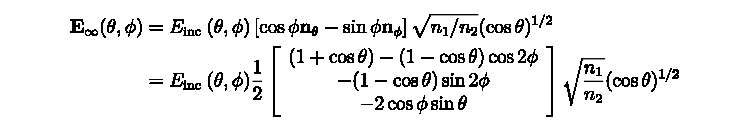

E_∞(θ,ϕ)==E_inc(θ,ϕ)1/2((1+cosθ)-(1-cosθ)cos2ϕ
-(1-cosθ)sin2ϕ
-2cosϕsinθ)√(n_1/n_2)(cosθ)^(1/2)

则三个分量分别表示为

x分量
E_(∞_x)(θ,ϕ)==E_inc(θ,ϕ)1/2 √(n_1/n_2)[(1+cosθ)-(1-cosθ)cos(2ϕ)]√cosθ
y分量
E_(∞_y)(θ,ϕ)==E_inc(θ,ϕ)1/2 √(n_1/n_2)[-(1-cosθ)sin(2ϕ)]√cosθ
z分量
E_(∞_z)(θ,ϕ)==E_inc(θ,ϕ)1/2 √(n_1/n_2)[-2cos(ϕ)sin(θ)]√cosθ

则 √cosθ为公钥的贡献部分（黄色背景），其余贡献用粉色背景表示。

最后的一点考虑

由于对于SU(2)相干光而言，k也是变量，故将这一项加入原来的SU(2)相干光的表达式中，定义Ψ_int^(SU(2))

-Graphics-

## 3. 代码详细解释

替换厄米多项式中的自变量（蓝色背景部分），并加入（粉色部分）

直接复制HoldForm的结果，无法算出结果，故需手动输入，为了加快计算将w[0]换为w_0

```mathematica
ff[θ_,ϕ_]:=1/2^(M/2)∑_(K=0)^M √Binomial[M,K] Exp[ⅈ K γ](Exp[(ⅈ((n+p K)+(m+(Q-p) K))α)/2]∑_(k=0)^((n+p K)+(m+(Q-p) K)) (Exp[ⅈ k α](Subscript[d, n+p K,m+(Q-p) K]^k)[β] √(2/L)Subscript[H, k][Cos[ϕ]]Subscript[H, (n+p K)+(m+(Q-p) K)-k][Sin[ϕ]]Exp[-((f Sin[θ])/Subscript[w, 0])^2])(ⅈ* Subscript[k, (n+p K)+(m+(Q-p) K)-k,k,l-P K]*f)/(2π)Exp[-ⅈ Subscript[k, (n+p K)+(m+(Q-p) K)-k,k,l-P K]*f]/(√(2^(((n+p K)+(m+(Q-p) K)-k)+k-1) π ((n+p K)+(m+(Q-p) K)-k)! k!) Subscript[w, 0]))
```

```mathematica
ff[1,1]
```

2^(-M/2) ∑_(K=0)^M ⅇ^(1/2 ⅈ (m+n+K p+K (-p+Q)) α+ⅈ K γ) √Binomial[M,K] ∑_(k=0)^(m+n+K p+K (-p+Q)) (ⅈ ⅇ^(ⅈ k α-(f^2 Sin[1]^2)/w_0^2-ⅈ f k_(-k+m+n+K p+K (-p+Q),k,l-K P)) f √(1/L) k_(-k+m+n+K p+K (-p+Q),k,l-K P) H_k[Cos[1]] H_(-k+m+n+K p+K (-p+Q))[Sin[1]] d_(n+K p,m+K (-p+Q))^k[β])/(√2 π^(3/2) w_0 √(2^(-1+m+n+K p+K (-p+Q)) k! (-k+m+n+K p+K (-p+Q))!))

将u加进去

用u代替(√2 f Sin[θ])/w[0]，完成积分后，再进行替换

```mathematica
fff=ff[θ,ϕ]/.{ Cos[ϕ]^n_->(u Cos[ϕ])^n,Sin[ϕ]^n_->(u Sin[ϕ])^n};
```

### 2. 计算分量

#### 1. x分量

##### 1. x分量的定义部分

补上E_(∞_x)(θ,ϕ)中引入的Cos[2ϕ]

```mathematica
ffx11=fff*Cos[2ϕ];
ffx12=fff;
```

和差化积

```mathematica
ffx21=ffx11//TrigReduce;
ffx22=ffx12//TrigReduce;
```

替换

```mathematica
ffx31=ffx21/.{ Cos[n_ ϕ]->2π ⅈ^n BesselJ[n,Subscript[k, n+m-k,k,l] ρ Sin[θ]]Cos[n φ],Sin[n_ ϕ]->2π ⅈ^n BesselJ[n,Subscript[k, n+m-k,k,l] ρ Sin[θ]]Sin[n φ]};
ffx32=ffx22/.{ Cos[n_ ϕ]->2π ⅈ^n BesselJ[n,Subscript[k, n+m-k,k,l] ρ Sin[θ]]Cos[n φ],Sin[n_ ϕ]->2π ⅈ^n BesselJ[n,Subscript[k, n+m-k,k,l] ρ Sin[θ]]Sin[n φ]};
```

二次替换

```mathematica
ffx41=ffx31/.{ Cos[ϕ]->2π ⅈ BesselJ[1,Subscript[k, n+m-k,k,l] ρ Sin[θ]]Cos[φ],Sin[ϕ]->2π ⅈ BesselJ[1,Subscript[k, n+m-k,k,l] ρ Sin[θ]]Sin[φ]};
ffx42=ffx32/.{ Cos[ϕ]->2π ⅈ BesselJ[1,Subscript[k, n+m-k,k,l] ρ Sin[θ]]Cos[φ],Sin[ϕ]->2π ⅈ BesselJ[1,Subscript[k, n+m-k,k,l] ρ Sin[θ]]Sin[φ]};
```

再把u换回来

```mathematica
ffx51=ffx41/.u->(√2 f Sin[θ])/Subscript[w, 0];
ffx52=ffx42/.u->(√2 f Sin[θ])/Subscript[w, 0];
```

再补上其他含θ的项

一共4项
-Graphics-
-Graphics-

注：需在

∫_0^(2π) ⅇ^(ⅈ x Cos[ϕ-φ])ⅆϕ=2 π 0Abs[x]

```mathematica
ffx6=Iconize[(ffx51(Cos[θ]-1)+ffx52(Cos[θ]+1)2π*BesselJ[0,Subscript[k, n+m-k,k,l] ρ Sin[θ]])*√Cos[θ] Sin[θ]]//CopyToClipboard
```

##### 1. x分量的计算

关于θ积分

将上面计算的结果复制下来，补全项后定义聚焦函数

-Graphics-
-Graphics-

```mathematica
gx[ρ_,φ_]:=NIntegrate[,{θ,0,1}]
```

```mathematica
gx[1,1]
```

-0.000163795-0.000142018 ⅈ

定义有分量的光强和相位

```mathematica
(*定义y分量的强度*)
Subscript[𝕀, x][ρ_,φ_]:=gx[ρ,φ]*gx[ρ,φ]*//Norm
(*定义y分量的相位*)
Subscript[𝒫, x][ρ_,φ_]:=Arg[gx[ρ,φ]]//Norm
```

```mathematica
Subscript[𝕀, x][1,1]//AbsoluteTiming
Subscript[𝒫, x][1,1]//AbsoluteTiming
```

{0.420657,4.69976×10^-8}

{0.20957,2.42728}

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, x][ρ,φ]//Norm},{ρ,0.0000001,0.1,.001},{φ,0,2π,.05}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, x][ρ,φ]//Norm},{ρ,0.0000001,0.1,.001},{φ,0,2π,.05}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

#### 2. y分量

##### 1. y分量的定义部分

补上E_(∞_y)(θ,ϕ)中引入的Sin[2ϕ]

```mathematica
ffy11=fff*Sin[2ϕ];
```

和差化积

```mathematica
ffy21=ffy11//TrigReduce;
```

替换

```mathematica
ffy31=ffy21/.{ Cos[n_ ϕ]->2π ⅈ^n BesselJ[n,Subscript[k, n+m-k,k,l] ρ Sin[θ]]Cos[n φ],Sin[n_ ϕ]->2π ⅈ^n BesselJ[n,Subscript[k, n+m-k,k,l] ρ Sin[θ]]Sin[n φ]};
```

二次替换

```mathematica
ffy41=ffy31/.{ Cos[ϕ]->2π ⅈ BesselJ[1,Subscript[k, n+m-k,k,l] ρ Sin[θ]]Cos[φ],Sin[ϕ]->2π ⅈ BesselJ[1,Subscript[k, n+m-k,k,l] ρ Sin[θ]]Sin[φ]};
```

再把u换回来

```mathematica
ffy51=ffy41/.u->(√2 f Sin[θ])/Subscript[w, 0];
```

再补上其他含θ的项

一共三项
-Graphics-
-Graphics-

```mathematica
ffy6=Iconize[(ffy51(Cos[θ]-1))*√Cos[θ] Sin[θ]]//CopyToClipboard
```

##### 2. y分量的计算

关于θ积分

将上面计算的结果复制下来，补全项后定义聚焦函数

-Graphics-
-Graphics-

```mathematica
gy[ρ_,φ_]:=NIntegrate[,{θ,0,1}]
```

```mathematica
gy[1,1]
```

-0.0000473581-0.0000646979 ⅈ

定义有分量的光强和相位

```mathematica
(*定义y分量的强度*)
Subscript[𝕀, y][ρ_,φ_]:=gy[ρ,φ]*gy[ρ,φ]*//Norm
(*定义y分量的相位*)
Subscript[𝒫, y][ρ_,φ_]:=Arg[gy[ρ,φ]]//Norm
```

```mathematica
Subscript[𝕀, y][1,1];//AbsoluteTiming
Subscript[𝒫, y][1,1];//AbsoluteTiming
```

{0.23076,Null}

{0.116501,Null}

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, y][ρ,φ]//Norm},{ρ,0.0000001,0.1,.002},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, y][ρ,φ]//Norm},{ρ,0.0000001,0.1,.002},{φ,0,2π,.1}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

#### 3. z分量

##### 1. z分量的定义部分

补上E_(∞_y)(θ,ϕ)中引入的Sin[2ϕ]

```mathematica
ffz11=fff*Cos[ϕ];
```

和差化积

```mathematica
ffz21=ffz11//TrigReduce;
```

替换

```mathematica
ffz31=ffz21/.{ Cos[n_ ϕ]->2π ⅈ^n BesselJ[n,Subscript[k, n+m-k,k,l] ρ Sin[θ]]Cos[n φ],Sin[n_ ϕ]->2π ⅈ^n BesselJ[n,Subscript[k, n+m-k,k,l] ρ Sin[θ]]Sin[n φ]};
```

二次替换

```mathematica
ffz41=ffz31/.{ Cos[ϕ]->2π ⅈ BesselJ[1,Subscript[k, n+m-k,k,l] ρ Sin[θ]]Cos[φ],Sin[ϕ]->2π ⅈ BesselJ[1,Subscript[k, n+m-k,k,l] ρ Sin[θ]]Sin[φ]};
```

再把u换回来

```mathematica
ffz51=ffz41/.u->(√2 f Sin[θ])/Subscript[w, 0];
```

再补上其他含θ的项

一共三项
-Graphics-
-Graphics-

```mathematica
ffz6=Iconize[(ffz51(-2Sin[θ]))*√Cos[θ] Sin[θ]]//CopyToClipboard
```

##### 2. z分量的计算

关于θ积分

将上面计算的结果复制下来，补全项后定义聚焦函数

-Graphics-
-Graphics-

```mathematica
gz[ρ_,φ_]:=NIntegrate[,{θ,0,1}]
```

```mathematica
gz[1,1]
```

-0.0000459965-0.000583161 ⅈ

定义有分量的光强和相位

```mathematica
(*定义y分量的强度*)
Subscript[𝕀, z][ρ_,φ_]:=gz[ρ,φ]*gz[ρ,φ]*//Norm
(*定义y分量的相位*)
Subscript[𝒫, z][ρ_,φ_]:=Arg[gz[ρ,φ]]//Norm
```

```mathematica
Subscript[𝕀, z][1,1];//AbsoluteTiming
Subscript[𝒫, z][1,1];//AbsoluteTiming
```

{0.425079,Null}

{0.208378,Null}

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, z][ρ,φ]//Norm},{ρ,0.0000001,0.1,.002},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, z][ρ,φ]//Norm},{ρ,0.0000001,0.1,.0002},{φ,0,2π,.1}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

#### 4. 计算总光强和总相位

```mathematica
Ε[ρ_,φ_]:=({{gx[ρ,φ]}, {gy[ρ,φ]}, {gz[ρ,φ]}})
𝕀[ρ_,φ_]:=Ε[ρ,φ]*Ε[ρ,φ]*//Norm
𝒫[ρ_,φ_]:=Arg[Ε[ρ,φ]]//Norm
```

```mathematica
Ε[1,1]
𝕀[1,1]
𝒫[1,1]
```

{{-0.000163795-0.000142018 ⅈ},{-0.0000473581-0.0000646979 ⅈ},{-0.0000459965-0.000583161 ⅈ}}

3.45464×10^-7

3.66938

```mathematica
data=ParallelTable[{ρ,φ,𝕀[ρ,φ]//Norm},{ρ,0.0000001,0.1,.002},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,𝒫[ρ,φ]//Norm},{ρ,0.0000001,0.1,.002},{φ,0,2π,.1}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium,ColorFunction->GrayLevel]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

# x偏振SU(2)光仿真紧聚焦仿真（z=0）

取z=0

#### 1. 输入参数

固定参数

```mathematica
(*令-Graphics-，以便于计算*)
c=π;
(*输入波长，单位um*)
λ=0.532;
Subscript[w, 0]=1000.λ;
```

可调参数

```mathematica
(*频率简并度，形如1/3*)
Ω=1/4;
(*计算2D谐振子的参数*)
P=N[Numerator[Rationalize@Ω]];
Q=N[Denominator[Rationalize@Ω]];
(*输入固有横模指数n*)
n=15.;
(*输入整数p*)
p=-1.;
(*输入固有横模指数m*)
m=30.;
(*输入固有纵模指数l*)
l=1.;
(*输入庞加莱球上的坐标(α,β)*)
α=π/2;
β=π/2;
(*输入初相位*)
γ=π/2;
(*输入相干叠加次数M*)
M=4.;
```

计算腔径，需首先清楚R的赋值

```mathematica
(*-Graphics-,令-Graphics-计算-Graphics-*)
R=.
L=1.;
R=NSolve[L/R==(Sin[Ω*π])^2,R]⟦1,1⟧/.Rule->Set;
```

#### 2. 定义函数

```mathematica
(*厄米多项式-Graphics-*)
Notation[Subscript[H, n_][x_] ⟺ HermiteH[n_,x_]]
(*锐利长度-Graphics-*)
Notation[Subscript[z, R] ⟺ √(L(R-L))]
(*Gouy相位-Graphics-*)
Notation[ϑ[z_] ⟺ ArcTan[z_/Subscript[z, R]]]
(*纵模频率间隔-Graphics-*)
Notation[Subscript[Δf, L] ⟺ c/2 L]
(*横模频率间隔-Graphics-*)
Notation[Subscript[Δf, T] ⟺ Subscript[Δf, L] ϑ[L]/π]
(*本征模频率-Graphics-*)
Notation[Subscript[f, n_,m_,l_] ⟺ l_*Subscript[Δf, L]+(n_+m_+1)*Subscript[Δf, T]]
(*本征模波数-Graphics-*)
Notation[Subscript[k, n_,m_,l_] ⟺ 2π Subscript[f, n_,m_,l_]/c]
Notation[Subscript[d, n_,m_]^k_[β_] ⟺ WignerD[{(n_+m_)/2,k_-(n_+m_)/2,(n_-m_)/2},β_]]
Notation[Subscript[Φ, n_,m_]^(HG)[x_,y_] ⟺ 1/(√(2^(m_+n_-1)π m_!n_!))1/Subscript[w, 0] Subscript[H, n_][(√2 x_)/Subscript[w, 0]]Subscript[H, m_][(√2 y_)/Subscript[w, 0]]Exp[-(x_^2+y_^2)/(Subscript[w, 0])^2]]
Notation[Subscript[ψ, n_,m_]^(HG)[x_,y_] ⟺ √(2/L)Subscript[Φ, n_,m_]^(HG)[x_,y_]Exp[-ⅈ(m_+n_+1)]]
Notation[Subscript[Ψ, n_,m_]^(HLG)[x_,y_,α_,β_] ⟺ Exp[ⅈ(n_+m_)/2 α_]∑_(k=0)^(n_+m_) Exp[ⅈ*k*α_]*Subscript[d, n_,m_]^k[β_]Subscript[ψ, k,n_+m_-k]^(HG)[x_,y_]]
Notation[Subscript[Ψ, n_,m_]^(SU(2))[x_,y_,α_,β_,γ_,M_] ⟺ 1/2^(M_/2)∑_(K=0)^M_ √Binomial[M_,K] Exp[ⅈ*K*γ_]*Subscript[Ψ, n_,m_]^(HLG)[x_,y_,α_,β_]]
(Subscript[Ψ, n+p*K,m+(Q-p)K]^(SU(2)))[1,1,α,β,γ,M]
```

3.79331×10^-21+3.0717×10^-21 ⅈ

```mathematica
Notation[Subscript[Ψ, int]^(SU(2))[x_,y_] ⟺ Subscript[Ψ, n+p*K,m+(Q-p)K]^(SU(2))[x_,y_,α,β,γ,M]]
Notation[Subscript[𝕀, int]^(SU(2))[x_,y_] ⟺ Subscript[Ψ, int]^(SU(2))[x_,y_]Subscript[Ψ, int]^(SU(2))[x_,y_]*]
(Subscript[𝕀, int]^(SU(2)))[2,2]
```

9.85436×10^-41+0. ⅈ

```mathematica
r=7500λ;
DensityPlot[#,{x,-r,r},{y,-r,r},PlotRange->All,Background->White,ColorFunction->GrayLevel,PlotPoints->200,ImageSize->{750,750},PlotLegends->#2,PlotLabel->#3]&@@@{{(Subscript[𝕀, int]^(SU(2)))[x,y]//Norm,,-Graphics-}}//Export["001.pdf",#]&//SystemOpen
```

## 2. 透镜参数设置

基于尼康100倍油浸物选取参数，参数为：

```mathematica
(*确保入射光为平行光*)
Subscript[w, 0]=1000λ;
(*经过验证，Subscript[ρ, max]≥7.5 Subscript[ω, 0]才可以覆盖入瞳*)
Subscript[ρ, max]=7.5 Subscript[w, 0];
Subscript[n, 1]=1.;
Subscript[n, 2]=1.518;
(*Subscript[计算θ, max]*)
NA=1.3;
Subscript[θ, max]=.;
Subscript[θ, max]=(Solve[NA==Subscript[n, 2] Sin[Subscript[θ, max]],Subscript[θ, max],InverseFunctions->True]/.Rule->Set)⟦1,1⟧
(*计算f*)
f=Subscript[ρ, max]/Tan[Subscript[θ, max]]
(*计算填充因子*)
Subscript[f, 0]=Subscript[ρ, max]/(f Sin[Subscript[θ, max]])
```

1.02824

2405.63

1.93675

#### 1. 透镜最大汇聚角

对于大NA物镜，不能认为

#### 2. 透镜焦距

tan(θ_max)=ρ_max/f
f=ρ_max/(tan(θ_max))

## 1. SU(2)光聚焦

定义Ψ_int^(SU(2))[θ,ϕ]，令z=0

```mathematica
(*-Graphics-*)
Notation[Subscript[Ψ, int]^(SU(2))[θ_,ϕ_] ⟺ N[Subscript[Ψ, n+p*K,m+(Q-p)K]^(SU(2))[f Cos[ϕ_] Sin[θ_],f Sin[θ_] Sin[ϕ_],α,β,γ,M]]]
```

```mathematica
Notation[Subscript[𝕀, int]^(SU(2))[θ_,ϕ_] ⟺ Subscript[Ψ, int]^(SU(2))[θ_,ϕ_]Subscript[Ψ, int]^(SU(2))[θ_,ϕ_]*]
```

```mathematica
{x,y,f,θ,ϕ}=.;
(Solve[{x==f Sin[θ]Cos[ϕ],y==f Sin[θ]Sin[ϕ]},{θ,ϕ},InverseFunctions->True]//Normal)⟦2,1;;2⟧
```

{θ→ArcSin[(-x^2/(√(x^2+y^2))-y^2/(√(x^2+y^2)))/f]+2 π C[2],ϕ→ArcTan[-x/(√(x^2+y^2)),-y/(√(x^2+y^2))]+2 π C[1]}

```mathematica
x=.;
y=.;
r=7500λ;
DensityPlot[#,{x,-r,r},{y,-r,r},PlotPoints->100,ColorFunction->GrayLevel,PlotRange->All,ImageSize->Large]&@(Subscript[𝕀, int]^(SU(2)))[ArcSin[(-x^2/(√(x^2+y^2))-y^2/(√(x^2+y^2)))/f],ArcTan[-x/(√(x^2+y^2)),-y/(√(x^2+y^2))]]//Export["00.pdf",#]&//SystemOpen
```

```mathematica
DensityPlot[#,{x,0,1},{y,0,2π},PlotRange->All,Background->White,ColorFunction->GrayLevel,PlotPoints->200,ImageSize->{750,750},PlotLegends->#2,PlotLabel->#3]&@@@{{(Subscript[𝕀, int]^(SU(2)))[x,y]//Norm,,-Graphics-}}
```

```mathematica
ArcTan[z,√(x^2+y^2)],ArcTan[x,y]
```

```mathematica
CoordinateTransform["Cartesian"->"Spherical",{x,y,z}]
```

```mathematica
ParallelTable[(Subscript[Ψ, int]^(SU(2)))[θ,0],{θ,0.,1.,0.1}]
```

```mathematica
{0.+0. ⅈ,3.5834489424938775*^-9+1.261269071214267*^-9 ⅈ,0.000016284511002659165+5.620071421911453*^-6 ⅈ,0.0000964877026753049-2.1161467156080368*^-6 ⅈ,-0.0001901666648816008-0.00013425920538916218 ⅈ,0.00006509628022754442+0.0003181141338120205 ⅈ,0.0001877350004396199-0.00034784471924694617 ⅈ,-0.00033157925677459457+0.00020925350883736543 ⅈ,0.00028010074076066204-0.00013594982174194544 ⅈ,-0.00021308107075346163+0.00012202292973244948 ⅈ,0.00011634953583421746-0.00013862998513189064 ⅈ}//Column
```

0.+0. ⅈ
3.58345×10^-9+1.26127×10^-9 ⅈ
0.0000162845+5.62007×10^-6 ⅈ
0.0000964877-2.11615×10^-6 ⅈ
-0.000190167-0.000134259 ⅈ
0.0000650963+0.000318114 ⅈ
0.000187735-0.000347845 ⅈ
-0.000331579+0.000209254 ⅈ
0.000280101-0.00013595 ⅈ
-0.000213081+0.000122023 ⅈ
0.00011635-0.00013863 ⅈ

```mathematica
Plot[(Subscript[Ψ, int]^(SU(2)))[θ,0.]//Norm,{θ,0.,1.}]//Export["2.pdf",#]&//SystemOpen
```

```mathematica
Plot[(Subscript[Ψ, int]^(SU(2)))[0.,ϕ]//Norm,{ϕ,0.,2.π}]//Export["2.pdf",#]&//SystemOpen
```

用HoldForm函数得出完整的表达式

```mathematica
HoldForm[(Subscript[Ψ, int]^(SU(2)))[θ,ϕ]]
```

1/2^(M/2)(∑_(K=0)^M √Binomial[M,K] Exp[ⅈ K γ] (Exp[1/2 ⅈ ((n+p K)+(m+(Q-p) K)) α] ∑_(k=0)^((n+p K)+(m+(Q-p) K)) (Exp[ⅈ k α] d_(n+p K,m+(Q-p) K)^k[β] (√(2/L) (H_k[(√2 (f Cos[ϕ] Sin[θ]))/w_0] H_((n+p K)+(m+(Q-p) K)-k)[(√2 (f Sin[θ] Sin[ϕ]))/w_0] Exp[-((f Cos[ϕ] Sin[θ])^2+(f Sin[θ] Sin[ϕ])^2)/w_0^2]) Exp[-ⅈ (((n+p K)+(m+(Q-p) K)-k)+k+1)]))/(√(2^(((n+p K)+(m+(Q-p) K)-k)+k-1) π ((n+p K)+(m+(Q-p) K)-k)! k!) w_0)))

```mathematica
ParametricPlot[{(Subscript[Ψ, int]^(SU(2)))[θ,0.]//Norm,(Subscript[Ψ, int]^(SU(2)))[0.,ϕ]//Norm},{θ,0.,1.},{ϕ,0.,2.π},ColorFunction->GrayLevel]//Export["2.pdf",#]&//SystemOpen
```

```mathematica
"1.pdf"//
```

```mathematica
""
```

化简表达式

挑出入射光表达式中含ϕ的部分，并用"…"表示，表示该部分仅对ϕ积分

挑出含ϕ的部分，是为了使用关于ϕ的积分恒等式

"…"=H_k[(√2 (f Cos[ϕ] Sin[θ]))/(w_0 √(1+((f Cos[θ])/z_R)^2))] H_((n+p K)+(m+(Q-p) K)-k)[(√2 (f Sin[θ] Sin[ϕ]))/(w_0 √(1+((f Cos[θ])/z_R)^2))] Exp[-((f Cos[ϕ] Sin[θ])^2+(f Sin[θ] Sin[ϕ])^2)/((w_0 √(1+((f Cos[θ])/z_R)^2))^2)]

化简后的积分部分

"…"=H_k[(√2 (f Cos[ϕ] Sin[θ]))/(w_0 √(1+((f Cos[θ])/z_R)^2))] H_((n+p K)+(m+(Q-p) K)-k)[(√2 (f Sin[θ] Sin[ϕ]))/(w_0 √(1+((f Cos[θ])/z_R)^2))] Exp[-(f  Sin[θ])^2/((w_0 √(1+((f Cos[θ])/z_R)^2))^2)]

发现第三项中的ϕ已被约去，故去掉第三项，引入ϕ的仅是厄米多项式

"…"=H_k[(√2 (f Cos[ϕ] Sin[θ]))/(w_0 √(1+((f Cos[θ])/z_R)^2))] H_((n+p K)+(m+(Q-p) K)-k)[(√2 (f Sin[θ] Sin[ϕ]))/(w_0 √(1+((f Cos[θ])/z_R)^2))]

化简后的表达式，积分部分用"…"代替

1/2^(M/2)(∑_(K=0)^M √Binomial[M,K] Exp[ⅈ K γ] (Exp[1/2 ⅈ ((n+p K)+(m+(Q-p) K)) α] ∑_(k=0)^((n+p K)+(m+(Q-p) K)) (Exp[ⅈ k α] d_(n+p K,m+(Q-p) K)^k[β] (√(2/L) ("…" Exp[-(f Sin[θ])^2/((w_0 √(1+((f Cos[θ])/z_R)^2))^2)]) Exp[1/c ⅈ (2 π f_((n+p K)+(m+(Q-p) K)-k,k,l-P K)) f Cos[θ] (1+(f^2 Sin[θ]^2)/(2 (L (-L+R)+f^2 Cos[θ]^2)))-ⅈ (((n+p K)+(m+(Q-p) K)-k)+k+1) ϑ[f Cos[θ]]]))/(√(2^(((n+p K)+(m+(Q-p) K)-k)+k-1) π ((n+p K)+(m+(Q-p) K)-k)! k!) (w_0 √(1+((f Cos[θ])/z_R)^2)))))

聚焦场积分公式对积分的贡献

E(ρ,φ,z)==(ikf e^-ikf)/(2π)∫_0^θ_max ∫_0^(2π) E_∞(θ,ϕ)e^ikzcosθ e^(ikρsinθcos(ϕ-φ))sinθdϕdθ

由于目前仅考虑聚焦平面上的场分布，故z=0，化简后的聚焦场积分公式

E(ρ,φ,z)==(ikf e^-ikf)/(2π)∫_0^θ_max ∫_0^(2π) E_∞(θ,ϕ)e^(ikρsinθcos(ϕ-φ))sinθdϕdθ

由于后面要用到两个积分恒等式 ，故先去掉恒等式中包含的部分

E(ρ,φ,z)==(ikf e^-ikf)/(2π)∫_0^θ_max ∫_0^(2π) E_∞(θ,ϕ)sinθdϕdθ

则聚焦场积分公式对积分仅贡献一个sinθ，不含ϕ分量

公式对积分的贡献

-Graphics-

E_∞(θ,ϕ)==E_inc(θ,ϕ)1/2((1+cosθ)-(1-cosθ)cos2ϕ
-(1-cosθ)sin2ϕ
-2cosϕsinθ)√(n_1/n_2)(cosθ)^(1/2)

则三个分量分别表示为，含ϕ部分用bold绿色标出

x分量
E_(∞_x)(θ,ϕ)==E_inc(θ,ϕ)1/2 √(n_1/n_2)[(1+cosθ)cos(0ϕ)-(1-cosθ)cos(2ϕ)]√cosθ
y分量
E_(∞_y)(θ,ϕ)==E_inc(θ,ϕ)1/2 √(n_1/n_2)[-(1-cosθ)sin(2ϕ)]√cosθ
z分量
E_(∞_z)(θ,ϕ)==E_inc(θ,ϕ)1/2 √(n_1/n_2)[-2sin(θ)cos(ϕ)]√cosθ

则 √cosθ为公钥的贡献部分（黄色背景），其余贡献用粉色背景表示。

最后的一点考虑

由于对于SU(2)相干光而言，k也是变量，故将这一项加入原来的SU(2)相干光的表达式中，定义Ψ_int^(SU(2))

-Graphics-

## 2. 代码详细解释

检查w_0是否改为w_0=270?

```mathematica
HoldForm[Subscript[w, 0]]
HoldForm[w[f Cos[θ]]]
Subscript[w, 0]
```

w_0

w_0 √(1+((f Cos[θ])/z_R)^2)

260.

替换厄米多项式中的自变量（蓝色背景部分），并加入（粉色部分）

-Graphics-

直接复制HoldForm的结果，无法算出结果，故需手动输入

```mathematica
ff[θ_,ϕ_]:=1/2^(M/2)∑_(K=0)^M √Binomial[M,K] Exp[ⅈ K γ](Exp[(ⅈ((n+p K)+(m+(Q-p) K))α)/2]∑_(k=0)^((n+p K)+(m+(Q-p) K)) (Exp[ⅈ k α](Subscript[d, n+p K,m+(Q-p) K]^k)[β] (√(2/L) (Subscript[H, k][ Cos[ϕ] ] Subscript[H, (n+p K)+(m+(Q-p) K)-k][ Sin[ϕ]] Exp[-(f*Sin[θ])^2/((Subscript[w, 0] √(1+((f Cos[θ])/Subscript[z, R])^2))^2)]) Exp[1/c ⅈ (2 π Subscript[f, (n+p K)+(m+(Q-p) K)-k,k,l-P K]) f Cos[θ] (1+(f^2  Sin[θ]^2)/(2 (L (-L+R)+f^2 Cos[θ]^2)))-ⅈ (((n+p K)+(m+(Q-p) K)-k)+k+1) ϑ[f Cos[θ]]]))(ⅈ* Subscript[k, (n+p K)+(m+(Q-p) K)-k,k,l-P K]*f)/(2π)Exp[-ⅈ Subscript[k, (n+p K)+(m+(Q-p) K)-k,k,l-P K]*f]/(√(2^(((n+p K)+(m+(Q-p) K)-k)+k-1) π ((n+p K)+(m+(Q-p) K)-k)! k!) (Subscript[w, 0] √(1+((f Cos[θ])/Subscript[z, R])^2))))

ff[1,1]
```

0.25 (((4.1188×10^-6+0.0000530841 ⅈ) ⅇ^((0.-39.2699 ⅈ) f-(2.50181×10^-6 f^2)/(1+0.291927 f^2)-(0.+46. ⅈ) ArcTan[0.540302 f]+(0.+21.2176 ⅈ) f (1+(f^2 Sin[1]^2)/(2 (1.+f^2 Cos[1]^2)))) f)/(√(1+0.291927 f^2))+((9.95517×10^-12-1.87119×10^-11 ⅈ) ⅇ^((0.-39.2699 ⅈ) f-(2.50181×10^-6 f^2)/(1+0.291927 f^2)-(0.+54. ⅈ) ArcTan[0.540302 f]+(0.+21.2176 ⅈ) f (1+(f^2 Sin[1]^2)/(2 (1.+f^2 Cos[1]^2)))) f)/(√(1+0.291927 f^2))+((5.28986×10^-18-3.29658×10^-18 ⅈ) ⅇ^((0.-39.2699 ⅈ) f-(2.50181×10^-6 f^2)/(1+0.291927 f^2)-(0.+62. ⅈ) ArcTan[0.540302 f]+(0.+21.2176 ⅈ) f (1+(f^2 Sin[1]^2)/(2 (1.+f^2 Cos[1]^2)))) f)/(√(1+0.291927 f^2))-((9.03412×10^-8+1.88545×10^-8 ⅈ) ⅇ^((0.-39.2699 ⅈ) f-(2.50181×10^-6 f^2)/(1+0.291927 f^2)-(0.+50. ⅈ) ArcTan[0.540302 f]+(0.+21.2176 ⅈ) f (1+(f^2 Sin[1]^2)/(2 (1.+f^2 Cos[1]^2)))) f)/(√(1+0.291927 f^2))+((7.66647×10^-16+7.38434×10^-16 ⅈ) ⅇ^((0.-39.2699 ⅈ) f-(2.50181×10^-6 f^2)/(1+0.291927 f^2)-(0.+58. ⅈ) ArcTan[0.540302 f]+(0.+21.2176 ⅈ) f (1+(f^2 Sin[1]^2)/(2 (1.+f^2 Cos[1]^2)))) f)/(√(1+0.291927 f^2)))

将u加进去

用u代替(√2 f Sin[θ])/(w_0 √(1+((f Cos[θ])/z_R)^2))，完成积分后，再进行替换

```mathematica
fff1=ff[θ,ϕ]/.{Cos[ϕ]->(u Cos[ϕ]),Sin[ϕ]->(u Sin[ϕ])};
```

为避免对ϕ和差化积导致的困难，先讲所有含θ的项替换掉

```mathematica
fff2=fff1/.{Sin[θ]->μ,Cos[θ]->ν};
```

## 3. 计算分量

#### 1. x分量

##### 1. x分量的定义部分

补上E_(∞_x)(θ,ϕ)中引入的Cos[2ϕ]

```mathematica
ffx11=fff2*Cos[2ϕ];
ffx12=fff2;
```

对ϕ和差化积

```mathematica
ffx21=ffx11//TrigReduce;
ffx22=ffx12//TrigReduce;
```

替换

```mathematica
ffx31=ffx21/.{ Cos[n_ ϕ]->2π ⅈ^n BesselJ[n,Subscript[k, n+m-k,k,l] ρ Sin[θ]]Cos[n φ],Sin[n_ ϕ]->2π ⅈ^n BesselJ[n,Subscript[k, n+m-k,k,l] ρ Sin[θ]]Sin[n φ]};
ffx32=ffx22/.{ Cos[n_ ϕ]->2π ⅈ^n BesselJ[n,Subscript[k, n+m-k,k,l] ρ Sin[θ]]Cos[n φ],Sin[n_ ϕ]->2π ⅈ^n BesselJ[n,Subscript[k, n+m-k,k,l] ρ Sin[θ]]Sin[n φ]};
```

二次替换

```mathematica
ffx41=ffx31/.{ Cos[ϕ]->2π ⅈ BesselJ[1,Subscript[k, n+m-k,k,l] ρ Sin[θ]]Cos[φ],Sin[ϕ]->2π ⅈ BesselJ[1,Subscript[k, n+m-k,k,l] ρ Sin[θ]]Sin[φ]};
ffx42=ffx32/.{ Cos[ϕ]->2π ⅈ BesselJ[1,Subscript[k, n+m-k,k,l] ρ Sin[θ]]Cos[φ],Sin[ϕ]->2π ⅈ BesselJ[1,Subscript[k, n+m-k,k,l] ρ Sin[θ]]Sin[φ]};
```

再把u、μ、ν换回来

```mathematica
ffx51=ffx41/.{u->(√2 f Sin[θ])/(Subscript[w, 0] √(1+((f Cos[θ])/Subscript[z, R])^2)),μ->Sin[θ],ν->Cos[θ]};
ffx52=ffx42/.{u->(√2 f Sin[θ])/(Subscript[w, 0] √(1+((f Cos[θ])/Subscript[z, R])^2)),μ->Sin[θ],ν->Cos[θ]};
```

再补上其他含θ的项

一共4项
-Graphics-
-Graphics-

注：需在

∫_0^(2π) ⅇ^(ⅈ x Cos[ϕ-φ])ⅆϕ=2 π 0Abs[x]

```mathematica
ffx6=Iconize[(ffx51(Cos[θ]-1)+ffx52(Cos[θ]+1)2π*BesselJ[0,Subscript[k, n+m-k,k,l] ρ Sin[θ]])*√Cos[θ] Sin[θ]]//CopyToClipboard
```

##### 2. x分量的计算

关于θ积分

将上面计算的结果复制下来，补全项后定义聚焦函数

```mathematica
gx[ρ_,φ_]:=NIntegrate[,{θ,0,0.5}]
```

```mathematica
gx[0.01,1]//AbsoluteTiming
```

{7.20264,-5.23373×10^-23-2.90316×10^-23 ⅈ}

定义x分量的光强和相位

```mathematica
(*定义x分量的强度*)
Subscript[𝕀, x][ρ_,φ_]:=gx[ρ,φ]*gx[ρ,φ]*//Norm
(*定义x分量的相位*)
Subscript[𝒫, x][ρ_,φ_]:=Arg[gx[ρ,φ]]//Norm
```

```mathematica
Subscript[𝕀, x][1,1]//AbsoluteTiming
Subscript[𝒫, x][1,1]//AbsoluteTiming
```

{17.3864,6.89379×10^-44}

{8.78378,0.284396}

##### 3. x分量绘图

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, x][ρ,φ]//Norm},{ρ,0.0000001,0.1,.001},{φ,0,2π,.05}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, x][ρ,φ]//Norm},{ρ,0.0000001,0.1,.001},{φ,0,2π,.05}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
(ListDensityPlot[#,PlotRange->All,ImageSize->Medium,ColorFunction->GrayLevel]&/@{data,data2})//Export["001.pdf",#]&
```

#### 2. y分量

##### 1. y分量的定义部分

补上E_(∞_x)(θ,ϕ)中引入的Cos[2ϕ]

```mathematica
ffy11=fff2*Sin[2ϕ];
```

对ϕ和差化积

```mathematica
ffy21=ffy11//TrigReduce;
```

替换

```mathematica
ffy31=ffy21/.{ Cos[n_ ϕ]->2π ⅈ^n BesselJ[n,Subscript[k, n+m-k,k,l] ρ Sin[θ]]Cos[n φ],Sin[n_ ϕ]->2π ⅈ^n BesselJ[n,Subscript[k, n+m-k,k,l] ρ Sin[θ]]Sin[n φ]};
```

二次替换

```mathematica
ffy41=ffy31/.{ Cos[ϕ]->2π ⅈ BesselJ[1,Subscript[k, n+m-k,k,l] ρ Sin[θ]]Cos[φ],Sin[ϕ]->2π ⅈ BesselJ[1,Subscript[k, n+m-k,k,l] ρ Sin[θ]]Sin[φ]};
```

再把u、μ、ν换回来

```mathematica
ffy51=ffy41/.{u->(√2 f Sin[θ])/(Subscript[w, 0] √(1+((f Cos[θ])/Subscript[z, R])^2)),μ->Sin[θ],ν->Cos[θ]};
```

再补上其他含θ的项

一共三项
-Graphics-
-Graphics-

```mathematica
ffy6=Iconize[(ffy51(Cos[θ]-1))*√Cos[θ] Sin[θ]]//CopyToClipboard
```

##### 2. y分量的计算

关于θ积分

将上面计算的结果复制下来，补全项后定义聚焦函数

```mathematica
gy[ρ_,φ_]:=NIntegrate[,{θ,0,0.5}]
```

```mathematica
gy[1,1]
```

-1.64993×10^-24+3.54194×10^-25 ⅈ

定义有分量的光强和相位

```mathematica
(*定义y分量的强度*)
Subscript[𝕀, y][ρ_,φ_]:=gy[ρ,φ]*gy[ρ,φ]*//Norm
(*定义y分量的相位*)
Subscript[𝒫, y][ρ_,φ_]:=Arg[gy[ρ,φ]]//Norm
```

```mathematica
Subscript[𝕀, y][1,1];//AbsoluteTiming
Subscript[𝒫, y][1,1];//AbsoluteTiming
```

{13.046,Null}

{6.68005,Null}

##### 3. y分量绘图

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, y][ρ,φ]//Norm},{ρ,0.0000001,0.1,.001},{φ,0,2π,.05}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, y][ρ,φ]//Norm},{ρ,0.0000001,0.1,.001},{φ,0,2π,.05}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
(ListDensityPlot[#,PlotRange->All,ImageSize->Medium,ColorFunction->GrayLevel]&/@{data,data2})//Export["002.pdf",#]&
```

#### 3. z分量

##### 1. z分量的定义部分

补上E_(∞_x)(θ,ϕ)中引入的Cos[2ϕ]

```mathematica
ffz11=fff2*Cos[ϕ];
```

对ϕ和差化积

```mathematica
ffz21=ffz11//TrigReduce;
```

替换

```mathematica
ffz31=ffz21/.{ Cos[n_ ϕ]->2π ⅈ^n BesselJ[n,Subscript[k, n+m-k,k,l] ρ Sin[θ]]Cos[n φ],Sin[n_ ϕ]->2π ⅈ^n BesselJ[n,Subscript[k, n+m-k,k,l] ρ Sin[θ]]Sin[n φ]};
```

二次替换

```mathematica
ffz41=ffz31/.{ Cos[ϕ]->2π ⅈ BesselJ[1,Subscript[k, n+m-k,k,l] ρ Sin[θ]]Cos[φ],Sin[ϕ]->2π ⅈ BesselJ[1,Subscript[k, n+m-k,k,l] ρ Sin[θ]]Sin[φ]};
```

再把u、μ、ν换回来

```mathematica
ffz51=ffz41/.{u->(√2 f Sin[θ])/(Subscript[w, 0] √(1+((f Cos[θ])/Subscript[z, R])^2)),μ->Sin[θ],ν->Cos[θ]};
```

再补上其他含θ的项

一共三项
-Graphics-
-Graphics-

```mathematica
ffz6=Iconize[(ffz51(-2Sin[θ]))*√Cos[θ] Sin[θ]]//CopyToClipboard
```

##### 2. z分量的计算

关于θ积分

将上面计算的结果复制下来，补全项后定义聚焦函数

```mathematica
gz[ρ_,φ_]:=NIntegrate[,{θ,0,0.5}]
```

```mathematica
gz[1,1]
```

5.20118×10^-24-2.51686×10^-24 ⅈ

定义有分量的光强和相位

```mathematica
(*定义y分量的强度*)
Subscript[𝕀, z][ρ_,φ_]:=gz[ρ,φ]*gz[ρ,φ]*//Norm
(*定义y分量的相位*)
Subscript[𝒫, z][ρ_,φ_]:=Arg[gz[ρ,φ]]//Norm
```

```mathematica
Subscript[𝕀, z][1,1];//AbsoluteTiming
Subscript[𝒫, z][1,1];//AbsoluteTiming
```

{16.0235,Null}

{8.17086,Null}

##### 3. z分量绘图

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, z][ρ,φ]//Norm},{ρ,0.0000001,0.1,.001},{φ,0,2π,.05}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, z][ρ,φ]//Norm},{ρ,0.0000001,0.1,.001},{φ,0,2π,.05}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
(ListDensityPlot[#,PlotRange->All,ImageSize->Medium,ColorFunction->GrayLevel]&/@{data,data2})//Export["003.pdf",#]&
```

#### 4. 计算总光强和总相位

##### 1. 定义函数

```mathematica
Ε[ρ_,φ_]:=({{gx[ρ,φ]}, {gy[ρ,φ]}, {gz[ρ,φ]}})
𝕀[ρ_,φ_]:=Ε[ρ,φ]*Ε[ρ,φ]*//Norm
𝒫[ρ_,φ_]:=Arg[Ε[ρ,φ]]//Norm
```

```mathematica
Ε[1,1]
𝕀[1,1]
𝒫[1,1]
```

{{2.52014×10^-22-7.36687×10^-23 ⅈ},{-1.64993×10^-24+3.54194×10^-25 ⅈ},{5.20118×10^-24-2.51686×10^-24 ⅈ}}

6.89379×10^-44

##### 2. 绘图

```mathematica
data=ParallelTable[{ρ,φ,𝕀[ρ,φ]//Norm},{ρ,0.0000001,0.1,.001},{φ,0,2π,.05}];
data2=ParallelTable[{ρ,φ,𝒫[ρ,φ]//Norm},{ρ,0.0000001,0.1,.001},{φ,0,2π,.05}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
(ListDensityPlot[#,PlotRange->All,ImageSize->Medium,ColorFunction->GrayLevel]&/@{data,data2})//Export["004.pdf",#]&
```

# 一些考虑

## 1. 一些问题

填充因子取值范围？

In order to make use of the full NA of the objective, the incident ﬁeld E_int has to ﬁll or overﬁll the back-aperture. 
为了充分 利用NA，入射场必须fill or overfill入瞳

所以我觉得填充因子应f_0≥1，但由于SU(2)光结构比较复杂，overfill可能会破坏光场结构，故选f_0≈0.9

在单位球上积分时，E_∞(θ,ϕ)是否含有z分量？

我认为不含有z分量，因为(3.52),(3.53),(3.54)式中，没用使用w[z]，而采用w_0，在w_0处，z=0

但此时，若令z=0，则破坏球坐标与直角坐标转换关系。

在2.12节中，我们认为，在各向同性煤质中，光场z的空间谱Ê在平面z=const（像面）只由z=0（物面）的空间谱决定，即

Ê(k_x,k_y;z)==Ĥ(k_x,k_y;z)Ê(k_x,k_y;0)

其中,Ĥ是传播子Ĥ(k_x,k_y;z)==e^(±i k_z z)

为何入射光为x偏振时，这样表述？

-Graphics-

入射光为线偏光时，入射光应定义为Ψ_int^(SU(2))[x,y,z](-sin(ϕ)
cos(ϕ)
0)，还是Ψ_int^(SU(2))[x,0,0]？

验证两者是否相同？

```mathematica
Notation[Subscript[Ψ, int]^(SU(2))[x_,y_,z_] ⟺ Subscript[Ψ, n+p*K,m+(Q-p)K,l-P*K]^(SU(2))[x_,y_,z_,α,β,γ,M]]
```

ϕ取多少？

为何入射光的偏振如此定义(-sin(ϕ)
cos(ϕ)
0)，为何没有z分量？

(x_∞,y_∞,z_∞)与参考球(ρ,θ,ϕ)的坐标变换关系坐标变换关系？

-Graphics-

ϕ仍未azimuthal angle，且为与x轴的夹角，θ仍为θ，且为与z正半轴的夹角，故坐标变换关系为

注：ρ为定值，ρ=f

w_0到底是束腰半径还是w[0]?

在Principles of Nano-Optics书中，聚焦因子中的w_0的确是束腰半径

-Graphics-

关于w_0的考虑？

为了确保SU(2)光作为入射光时近似是入射光，故舍弃原先定义w_0的方式，采用w_0=260，约为